# Voronoi Relaxation

```mathematica
vmesh=VoronoiMesh[RandomReal[{-1,1},{20,2}]];
Dynamic[
pts=PropertyValue[{vmesh,2},MeshCellCentroid];
If[Length@pts<200,AppendTo[pts,{0,0}]];
vmesh=VoronoiMesh[pts,{{-1,1},{-1,1}}]
];
```

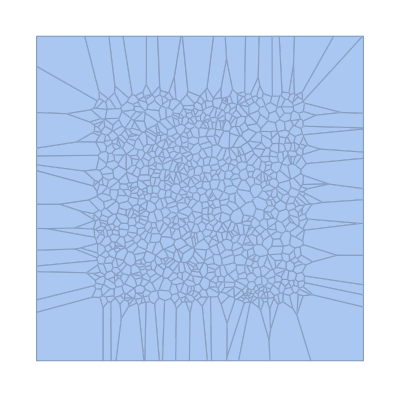

```mathematica
vmesh=VoronoiMesh[RandomReal[{-1,1},{1000,2}]]
```

```mathematica
Do[pts=PropertyValue[{vmesh,2},MeshCellCentroid];
vmesh=VoronoiMesh[pts,{{-1,1},{-1,1}}],
100]
```

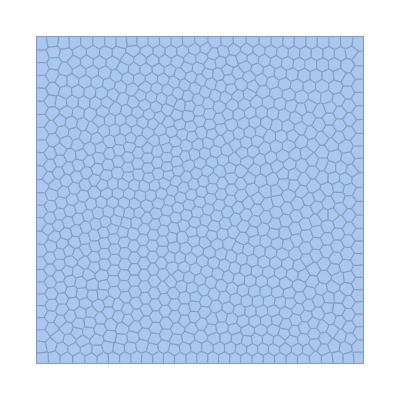

```mathematica
vmesh
```

```mathematica
polys=MeshPrimitives[vmesh,2];
```

```mathematica
Needs["IGraphM`"]
g=IGMeshCellAdjacencyGraph[vmesh,2];
adjMat=AdjacencyMatrix[g]
```

IGraph/M 0.3.108 (December 17, 2018)

Evaluate IGDocumentation[] to get started.

SparseArray[…]

```mathematica
posT=Flatten@Position[RegionWithin[Disk[],#]&/@polys,True];
```

```mathematica
insidePolys=Pick[polys,RegionWithin[Disk[],#]&/@polys,True];
```

```mathematica
posF=Flatten@Position[RegionWithin[Disk[],#]&/@polys,False];
```

{{281,224,510,654,769,812,823},{583,272,302,507,683,744,777},{187,202,816,843,856,920}}

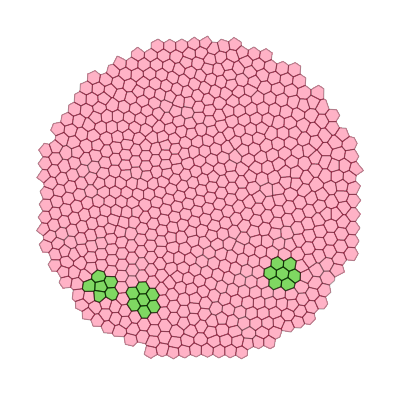

```mathematica
clusters=Prepend[Flatten@adjMat[[#]]["ColumnIndices"]~Complement~posF,#]&/@RandomChoice[posT,3]
Show[
Graphics[{EdgeForm[Black],XYZColor[1,0,0,0.30],#}]&/@insidePolys,
Graphics[{EdgeForm[Black],XYZColor[0,1,0,0.50],polys[[#]]&/@clusters}]
]
```

{r→0.0319864}

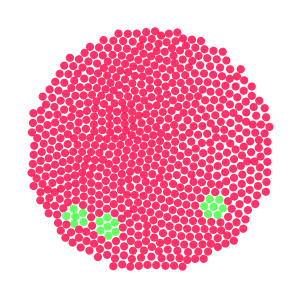

```mathematica
sol=Cases[Solve[π r^2 ==Min[RegionMeasure /@ insidePolys],r],PatternSequence[r->x_/;x∈PositiveReals],{2}]
posdel=Position[insidePolys,Apply[Alternatives]@Flatten[polys[[#]]&/@clusters]];
centroids=RegionCentroid/@Delete[insidePolys,posdel];
clustercentroids=RegionCentroid/@polys[[Flatten@clusters]];
Graphics[{XYZColor[0,1,0,0.6],Disk[#,r/.sol]&/@clustercentroids,XYZColor[1,0,0,0.8],Disk[#,r/.sol]&/@centroids}]
```

```mathematica
Append[{clustercentroids},centroids]
```

{{{-0.247263,0.0857153},{-0.240317,0.0138397},{-0.192047,0.0619655},{-0.243687,0.151194},{-0.307182,0.106498},{-0.299502,0.0382156},{-0.183227,0.130592},{-0.0891733,-0.0893935},{-0.0251662,-0.0770654},{-0.117671,-0.0293625},{-0.0563285,-0.0195689},{-0.160739,-0.0802095},{-0.134466,-0.139658},{-0.0602044,-0.152205},{-0.0955329,0.672686},{-0.14868,0.631166},{-0.0806948,0.731199},{-0.0832927,0.612764},{-0.0263152,0.672132},{-0.153358,0.708208}},{{-0.155501,-0.454371},{0.0850289,-0.405413},{-0.278338,-0.244523},{-0.636747,0.362836},{0.120082,-0.306814},{-0.389902,-0.649081},{0.507956,0.230666},{-0.833406,-0.348414},{-0.433282,0.280157},{-0.583741,-0.437015},{-0.5143,-0.606391},{-0.603843,0.0857783},{0.457338,0.390864},{-0.861811,0.380851},{0.61373,-0.125526},{-0.496026,-0.485917},{0.263514,-0.00785707},{0.265798,-0.601822},{0.292372,0.467189},{0.376258,0.736421},{0.737413,-0.144295},{0.448721,0.520387},{0.478346,-0.682932},{0.245371,0.746964},{-0.396195,-0.00375771},{0.589114,0.292694},{-0.373264,0.494933},{0.379275,-0.410056},{-0.53243,0.429795},{0.672189,-0.338728},{0.29157,-0.712241},{0.0641493,0.205451},{0.857118,0.279906},{-0.143131,0.0281502},{0.57443,0.15922},{0.355554,0.308435},{-0.428454,0.0383369},{-0.262437,0.566489},{0.581765,-0.536628},{-0.272561,0.277392},{0.245569,-0.487783},{0.00284728,-0.128697},{-0.215355,-0.78322},{0.517817,0.459529},{0.215889,0.565786},{-0.104373,0.20953},{0.0339444,0.0475788},{-0.0217442,0.608384},{0.354723,-0.111925},{-0.804656,0.0641255},{0.45687,0.0478614},{-0.387005,-0.74566},{-0.447046,-0.843619},{-0.160678,-0.335521},{-0.692473,-0.502613},{-0.553846,0.531706},{0.0390575,-0.602984},{0.733812,0.188553},{-0.272474,-0.415768},{0.528308,0.696017},{-0.460102,0.796771},{-0.81192,-0.0989651},{-0.0302454,-0.685986},{0.243814,-0.317768},{-0.396585,-0.458769},{0.23703,0.347126},{-0.296502,0.863557},{-0.494702,-0.204617},{0.172849,-0.0205039},{-0.741115,0.163577},{0.586229,-0.310865},{-0.648942,-0.332307},{0.913677,0.20377},{-0.156077,-0.234933},{-0.659128,0.580875},{0.48298,-0.10768},{0.0662113,0.812376},{-0.21861,0.710336},{0.43206,-0.265461},{-0.501727,-0.73583},{0.482631,-0.232979},{-0.208556,0.64713},{-0.279459,0.694638},{0.10497,0.857637},{0.0229973,0.862264},{0.518431,-0.0615404},{-0.62135,0.689263},{-0.108476,-0.19855},{-0.186995,-0.179473},{0.182008,-0.154673},{0.113312,-0.114318},{-0.616741,-0.383038},{0.592262,-0.247052},{-0.639809,0.470672},{-0.67948,0.179692},{-0.505515,0.699952},{-0.732162,0.227532},{-0.851499,0.168577},{0.0000169116,0.799393},{-0.0478885,0.856561},{0.113894,-0.0474925},{-0.537403,-0.251757},{-0.787543,0.270455},{0.197165,0.397628},{-0.333551,0.660447},{-0.335343,0.735767},{-0.355967,-0.504817},{0.561906,-0.75425},{-0.321167,0.801431},{-0.118119,0.847828},{0.281,-0.363619},{-0.0144877,-0.741992},{-0.0870547,-0.727623},{-0.802952,-0.167647},{-0.864962,-0.135645},{-0.433775,0.850766},{0.539476,0.629304},{-0.910875,-0.0912977},{-0.712476,0.463154},{-0.293618,-0.478842},{0.151373,-0.810057},{0.187525,-0.869771},{0.265475,0.237239},{0.264373,-0.872496},{-0.793869,-0.237265},{-0.110148,0.318727},{-0.0638677,0.255463},{-0.737583,-0.188479},{-0.267591,0.761001},{0.137608,0.914647},{0.7927,0.200085},{0.742212,0.254673},{-0.496646,0.558028},{-0.00149096,-0.555848},{-0.756542,-0.522879},{-0.727934,-0.446432},{-0.387186,-0.814518},{0.708826,0.0859843},{-0.10099,-0.35098},{0.783796,0.0746121},{0.52375,0.0469304},{0.498018,-0.457854},{0.480574,-0.00831224},{0.211044,0.911669},{0.172169,0.852159},{0.0451458,0.687537},{0.0529539,-0.737341},{-0.780072,0.451941},{-0.755158,0.516175},{-0.77008,0.334758},{-0.717993,0.288888},{0.621862,-0.437118},{-0.790781,0.00208371},{-0.0744582,-0.906929},{0.690401,-0.468724},{-0.857338,0.023548},{0.664725,0.0404693},{0.361534,-0.176545},{0.0158969,0.555399},{-0.0270597,0.045401},{0.00357619,0.107491},{0.226294,0.624045},{-0.649056,0.303593},{0.284758,0.580967},{0.608305,-0.184913},{0.445513,-0.800992},{0.204541,0.796257},{0.0804452,-0.801605},{0.331897,-0.760914},{0.404754,-0.751282},{0.394805,0.849212},{-0.469329,0.437771},{0.581306,0.427203},{-0.557027,-0.181982},{0.57513,0.496682},{-0.442281,0.379988},{0.849014,0.0773121},{0.906294,-0.303498},{0.847031,-0.342582},{0.816001,0.0122866},{-0.913759,0.0600963},{-0.550359,0.218325},{-0.181168,-0.840222},{0.902701,-0.102155},{-0.364633,0.384771},{-0.690073,-0.391492},{0.746031,-0.429306},{0.624352,0.541301},{-0.056203,0.551319},{-0.178185,-0.511531},{-0.445964,0.66105},{-0.316511,0.237853},{0.685542,0.14654},{0.308358,-0.481486},{0.377335,-0.474129},{-0.427063,0.0966362},{-0.232746,0.508996},{0.408556,-0.85812},{0.795922,-0.386301},{0.813309,-0.460572},{-0.703767,0.112017},{0.906109,-0.237625},{-0.568997,-0.111775},{-0.227574,-0.0609526},{-0.582123,-0.0435829},{0.630955,0.183531},{0.157189,-0.628076},{0.185733,-0.224946},{0.243667,-0.186359},{0.299444,-0.146789},{-0.277166,-0.109262},{0.30525,-0.218942},{0.347938,0.600363},{-0.909663,0.207995},{-0.000597358,-0.912122},{-0.12883,0.0917407},{-0.145964,-0.694587},{0.818185,0.339495},{0.815253,0.461867},{-0.194114,0.447853},{0.0762793,0.264697},{0.640259,0.397668},{-0.285566,-0.906044},{-0.716671,0.000504382},{0.702484,0.436315},{0.143435,-0.362152},{-0.765227,-0.0531094},{0.674221,0.585923},{-0.68315,0.520117},{-0.203105,-0.64836},{0.584629,-0.634805},{0.790987,-0.174557},{-0.683851,-0.137364},{0.737114,0.559605},{0.7827,-0.244329},{-0.139657,-0.619801},{-0.747808,-0.120005},{-0.619733,-0.159302},{-0.701054,-0.643054},{-0.580337,0.33732},{-0.918431,-0.177559},{0.421498,-0.364998},{-0.0719441,-0.586921},{0.286075,0.912551},{-0.447682,0.7335},{-0.0208891,-0.623867},{0.13684,-0.561318},{-0.3904,-0.130851},{0.534087,-0.346973},{0.124331,-0.246128},{-0.115518,0.153559},{-0.257312,-0.600892},{-0.185203,0.842852},{0.189908,-0.757169},{0.060111,-0.150524},{0.237209,0.686886},{-0.124945,0.441946},{-0.505744,0.490883},{0.01008,-0.799131},{-0.15351,0.383391},{0.401876,-0.570801},{-0.717121,-0.327517},{0.438918,-0.0571547},{-0.634831,-0.67787},{0.399335,0.261431},{0.389234,0.484363},{-0.671479,-0.205887},{0.546006,-0.581213},{0.175223,0.153597},{0.168641,0.658582},{0.719107,-0.0853029},{0.756162,-0.498966},{-0.247281,0.8257},{0.206443,-0.578401},{0.65207,-0.647979},{-0.0856382,0.0416815},{-0.325912,0.588295},{0.408276,0.0841641},{-0.596105,0.0228135},{0.684479,0.221815},{0.360438,0.130907},{-0.604485,-0.231322},{0.120238,0.513725},{0.484492,0.105664},{-0.844323,-0.410849},{-0.384245,-0.272262},{0.125778,0.388752},{0.150009,-0.920617},{-0.649423,-0.0175689},{-0.181309,0.325778},{-0.307833,0.17226},{-0.571534,-0.640965},{0.476234,0.656748},{-0.387627,0.62616},{0.446922,0.210737},{-0.364238,-0.344683},{-0.19075,-0.289183},{-0.331181,-0.853507},{0.192779,-0.519051},{0.284578,0.795672},{-0.478959,-0.371134},{-0.0192914,0.495417},{-0.103715,-0.486114},{0.505474,0.802867},{0.223729,0.100304},{-0.320979,-0.292926},{0.664074,-0.224435},{-0.163923,0.507616},{0.49321,0.338864},{-0.522545,-0.424616},{0.103939,0.145938},{0.53083,0.290617},{0.553502,-0.410137},{0.276796,0.052357},{0.460355,0.281682},{-0.0398895,-0.37931},{0.240877,-0.116652},{-0.49335,0.117503},{-0.337113,-0.0840482},{0.789266,-0.0999857},{-0.0576579,-0.233799},{0.00244962,-0.262353},{0.0612591,-0.283322},{-0.571427,-0.567216},{-0.849882,0.446811},{0.0305833,0.158704},{-0.251895,-0.306322},{-0.371334,0.196896},{0.052325,0.501494},{-0.635096,-0.603218},{-0.475451,0.32306},{0.484291,-0.39027},{0.103965,0.639578},{0.426954,0.699906},{-0.432329,0.157638},{-0.498529,-0.546852},{-0.409445,-0.389488},{0.228388,-0.0537548},{0.258958,0.518418},{0.128293,0.0306474},{0.155008,0.451821},{0.228789,-0.923772},{-0.272825,-0.744309},{-0.0403638,-0.450089},{-0.906641,0.280477},{0.254788,-0.424144},{0.396881,0.4082},{-0.535851,0.293623},{-0.543969,0.0727169},{-0.698089,-0.570687},{0.341321,0.43815},{0.319562,-0.420156},{0.415983,0.625407},{-0.0931071,0.498271},{-0.572843,0.731251},{-0.248729,0.213761},{-0.629945,-0.526782},{-0.396836,0.330772},{-0.206947,-0.718146},{0.890449,0.142698},{-0.0836862,0.378407},{0.913134,0.0815892},{0.84573,-0.131881},{-0.00272166,-0.193606},{-0.0531462,-0.520536},{0.0870606,0.444801},{0.769364,-0.0365698},{-0.490923,0.249731},{0.0177108,0.438035},{-0.432071,0.219238},{-0.294921,0.384912},{-0.26932,-0.673381},{-0.485038,0.0491545},{0.565915,-0.474869},{0.352112,0.793171},{-0.455276,-0.439305},{0.0982961,0.32584},{-0.09283,0.911839},{-0.124735,-0.550727},{0.33026,-0.00404046},{-0.851508,-0.283487},{0.472491,-0.571195},{0.783869,-0.312789},{0.345714,0.061097},{-0.0537409,0.437604},{0.766652,-0.565586},{0.153463,0.0899591},{-0.298302,-0.357884},{0.293776,0.115348},{0.130137,0.208735},{0.193528,-0.449495},{-0.381256,0.555275},{0.310965,0.181911},{0.890499,0.33823},{0.338377,0.368411},{-0.250127,0.332254},{-0.340636,-0.0131791},{0.0550685,0.37879},{0.520722,0.397641},{0.481085,0.739399},{0.0605959,0.75181},{0.419015,-0.691919},{0.168302,0.334937},{0.556257,0.566145},{-0.49424,-0.665932},{-0.166302,0.907774},{0.185865,0.511697},{0.43211,0.147441},{0.147261,0.272016},{0.646489,-0.286062},{0.655188,-0.0787644},{0.704456,-0.601405},{0.222315,-0.646163},{0.509921,0.522593},{0.244227,0.167246},{0.379137,0.195804},{-0.56501,-0.708266},{0.439266,-0.627646},{0.374258,-0.0543153},{-0.217735,-0.900199},{-0.780598,-0.306752},{-0.0137646,0.37607},{0.329842,-0.589218},{0.366889,-0.244888},{0.824816,0.140459},{0.555183,0.103051},{-0.658911,-0.27209},{0.231651,-0.704636},{0.121372,-0.746432},{-0.324275,-0.62564},{0.0743936,-0.916823},{0.11439,0.710044},{0.360978,0.669796},{0.131075,-0.49436},{-0.803216,0.388844},{-0.198438,0.77303},{0.692665,0.295659},{0.00961146,-0.335333},{-0.308417,-0.553736},{-0.394518,-0.203322},{-0.633531,-0.0883152},{0.386865,-0.308406},{-0.398663,-0.0632609},{0.321519,0.855086},{-0.914322,-0.260463},{-0.322333,-0.782647},{0.0609916,-0.217092},{-0.445501,-0.167074},{-0.332913,-0.220808},{0.846255,-0.205586},{0.610443,-0.70229},{0.726237,-0.20945},{-0.221618,-0.233378},{0.510884,-0.630371},{-0.192968,-0.577447},{0.483128,-0.167818},{0.0695544,-0.349897},{0.752161,0.481363},{0.140667,-0.4272},{0.703881,0.36775},{-0.698377,-0.0677096},{-0.453319,-0.095765},{0.640111,0.332576},{0.372285,-0.636937},{0.197721,0.219383},{0.0260109,0.311784},{0.725392,0.634024},{-0.22373,0.390378},{0.843188,0.398338},{0.755639,0.326607},{0.399712,0.558473},{-0.0867558,-0.656069},{0.0723624,-0.000441245},{-0.330146,-0.155805},{-0.211723,-0.124762},{0.0948112,-0.61339},{0.247412,-0.254952},{-0.184443,-0.0155671},{0.635213,0.255682},{0.166059,-0.69319},{-0.284832,-0.0369487},{-0.529738,0.00139847},{-0.515968,-0.0664351},{-0.722791,0.571746},{0.338717,-0.868602},{0.856885,-0.414747},{0.90503,-0.170062},{-0.741295,0.0620899},{-0.638067,0.130966},{-0.265856,0.45064},{0.696145,-0.53768},{0.258727,-0.765853},{-0.368014,0.13047},{0.351943,-0.530557},{-0.243736,-0.526044},{0.0724793,-0.466977},{-0.441092,0.586396},{-0.0172527,0.916469},{-0.371465,0.266751},{0.689335,0.511499},{0.734249,-0.357019},{-0.331933,0.444813},{-0.098886,-0.416537},{0.910329,-0.0376567},{0.00935461,-0.0179219},{-0.611755,0.194272},{-0.496195,0.18198},{-0.913544,0.13555},{0.84406,-0.273955},{0.884793,0.0177525},{-0.405294,0.439922},{0.638589,0.468003},{-0.506284,-0.135837},{0.370786,-0.809147},{0.354676,-0.69951},{0.0402939,-0.85827},{0.659802,0.656982},{0.178328,0.729718},{0.295003,0.651052},{-0.207124,0.265678},{-0.597297,0.265025},{-0.432595,-0.320348},{-0.0617875,0.111357},{0.422509,-0.197174},{0.0839124,0.570195},{0.596275,0.0478271},{0.695677,-0.0221898},{0.679447,-0.40261},{0.635284,-0.505167},{-0.0348747,-0.85123},{-0.145777,-0.904563},{-0.700733,0.350422},{0.100496,-0.680234},{-0.820499,0.503421},{0.0386219,0.623359},{-0.0106364,0.735974},{0.246962,0.852957},{0.625472,-0.0164906},{-0.127565,0.562542},{0.556421,-0.0080016},{0.51131,-0.520146},{0.436465,-0.43921},{-0.110324,-0.84164},{0.758345,0.1326},{-0.0503523,-0.305792},{0.740687,0.02532},{-0.793843,-0.461772},{0.0130327,-0.489262},{-0.501825,0.62613},{0.800345,0.268828},{-0.140878,0.262445},{0.297691,-0.817413},{0.330272,0.247751},{-0.0402994,0.31424},{-0.726061,-0.257028},{0.218027,0.284381},{0.223289,-0.818083},{0.11312,-0.8631},{-0.166582,-0.396867},{-0.912566,-0.0170673},{-0.737455,0.400606},{0.607773,0.612841},{-0.0667269,-0.790199},{0.344839,-0.354116},{-0.85972,-0.211061},{-0.13462,0.779621},{-0.366034,0.851453},{0.518624,-0.803785},{0.542066,-0.692544},{-0.378401,-0.574232},{-0.390216,0.701564},{0.227372,0.454549},{-0.850233,0.243488},{-0.504011,-0.306091},{-0.0668835,0.793504},{-0.795753,0.20093},{-0.857054,0.0999479},{-0.559255,0.662301},{-0.663764,0.241695},{-0.516967,0.768913},{-0.668367,0.414368},{0.542498,-0.203985},{-0.57808,0.474851},{-0.551224,-0.361316},{0.173125,-0.0894551},{0.122951,-0.181436},{-0.562967,0.59284},{-0.616976,0.624917},{0.582711,-0.0708638},{0.0618715,0.913471},{0.591868,0.684285},{-0.268982,0.629461},{0.526213,-0.277426},{-0.455252,-0.777164},{0.469281,-0.31836},{0.558405,0.755169},{0.547578,-0.134486},{-0.684317,0.639272},{0.915094,0.271062},{-0.614926,0.538967},{-0.593191,0.408231},{-0.585899,-0.302414},{-0.788617,0.125843},{-0.452165,-0.251715},{-0.240015,0.90283},{0.276618,0.397809},{-0.4308,-0.522779},{0.483239,-0.744422},{-0.391672,0.78171},{0.311759,-0.292059},{-0.848833,-0.0475744},{-0.22452,-0.368233},{-0.341196,-0.419819},{-0.221293,-0.452449},{0.289026,0.310348},{0.0699456,-0.538613},{-0.143932,-0.772176},{-0.112768,-0.280204},{0.437386,-0.509574},{-0.196992,0.575845},{0.034756,-0.671505},{0.418804,-0.126207},{-0.177868,0.198747},{0.131549,0.785312},{-0.561049,0.144763},{0.0498998,-0.075369},{-0.647519,-0.45258},{0.274881,-0.54199},{-0.325623,0.320586},{-0.84166,0.316732},{-0.308407,0.514939},{-0.363012,0.0603338},{0.633218,-0.579983},{-0.665576,0.0535515},{0.571692,0.224835},{-0.263461,-0.177102},{0.0793811,0.0877095},{0.333401,0.525487},{0.00356591,0.240667},{0.572141,0.356329},{-0.462503,-0.0234448},{0.299476,-0.653219},{0.769534,0.402439},{0.183711,-0.297378},{0.0200455,-0.412255},{0.85367,0.210665},{-0.336667,-0.700966},{0.402209,0.00925726},{0.630768,0.107459},{-0.444571,-0.603638},{-0.261121,-0.83315},{-0.44035,0.509638},{0.453071,0.455017},{0.674558,-0.152389},{0.843537,-0.0539253},{0.308777,0.723557},{0.477884,0.585754},{0.414778,0.337326},{-0.0382247,0.179695},{0.718271,-0.281473},{0.205225,0.0344745},{-0.564423,-0.498341},{0.507303,0.166359},{0.299398,-0.0710529},{0.152926,0.584659},{0.428561,0.784407},{-0.769004,-0.384894},{0.205517,-0.375988},{-0.434527,-0.698021},{0.610891,-0.36934},{-0.519046,0.37025}}}

```mathematica
pad[δ_][{min_,max_}]:={min,max}+δ(max-min){-1,1}

VoronoiCells[pts_]/;MatrixQ[pts,NumericQ]&&2≤Last[Dimensions[pts]]≤3:=Block[{bds,dm,conn,adj,lc,pc,cpts,hpts,hns,hp,vcells},bds=pad[.1]/@MinMax/@Transpose[pts];
dm=DelaunayMesh[pts];
conn=dm["ConnectivityMatrix"[0,1]];
adj=conn.Transpose[conn];
lc=conn["MatrixColumns"];
pc=adj["MatrixColumns"];
cpts=MeshCoordinates[dm];
vcells=Table[hpts=PropertyValue[{dm,{1,lc[[i]]}},MeshCellCentroid];
hns=Transpose[Transpose[cpts[[DeleteCases[pc[[i]],i]]]]-cpts[[i]]];
hp=MapThread[HalfSpace,{hns,hpts}];
BoundaryDiscretizeGraphics[#,PlotRange->bds]&/@hp,{i,MeshCellCount[dm,0]}];
AssociationThread[cpts,RegionIntersection@@@vcells]]
```

```mathematica
SeedRandom[10000];
pts=RandomReal[{-1,1},{100,3}];
vc=VoronoiCells[pts];
```

```mathematica
Show[MapIndexed[BoundaryMeshRegion[#,MeshCellStyle->{1->{Black,Thick},2->{ColorData[112][First[#2]]}}]&,Values[vc]]
]
```

-Graphics3D-

```mathematica
Do[
vc=Values[vc];
pts=Map[First@PropertyValue[{#,3},MeshCellCentroid]&,vc];
vc=VoronoiCells[pts],
5];
```

```mathematica
Show@MapIndexed[BoundaryMeshRegion[#,MeshCellStyle->{1->{Black,Thick},2->{Opacity[0.2],ColorData[112][First[#2]]}}]&,Values[vc]]
```

-Graphics3D-